```mathematica
Msol := 1989*10^(30) (*en gramos*)
m0 :=10^4*Msol
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
mb := m0*ab
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

```mathematica
Mandin[x_]:= mb*(1+x^2)^(1/2)
```

```mathematica
g[x_]:=(σ*x^3)/(3*(x^2+1) ^(3/2))
Manac[x_] := 1/(1/m0-(g[x]-g[xi]))
```

```mathematica
Plot[{Mandin[x],Manac[x]},{x,-xi,xi},PlotLegends->{"dinámica","acreción"}]
```

-Graphics-

```mathematica
N[Manac[xi]]
```

1.989×10^37

```mathematica
prueba[x_]:=Mandin[x]/Manac[x]
```

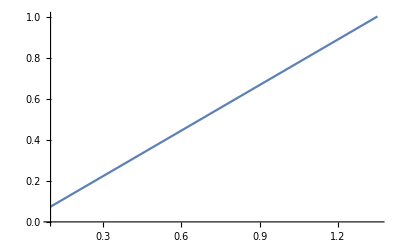

```mathematica
Plot[prueba[x], {x, 10^7, xi}]
```

```mathematica
prueba[x]
```

```mathematica
mb √(1+x^2) (1/m0-(x^3 σ)/(3 (1+x^2)^(3/2))+(xi^3 σ)/(3 (1+xi^2)^(3/2)))
```

```mathematica
NSolve[prueba[x] -0.1== 0, x]
```

{{x→3.796×10^-9-1. ⅈ},{x→3.796×10^-9-1. ⅈ},{x→3.796×10^-9+1. ⅈ},{x→3.796×10^-9+1. ⅈ}}

```mathematica
N[prueba[0]]
```

8.1692×10^-9

```mathematica
N[prueba[1.3495276653171344*^7]]
```

0.1

```mathematica
N[prueba[-xi]]
```

1.20676

```mathematica
f[x_]:= prueba[x]-0.1
FindRoot[f[x], {x,-1.4*10^7}]
```

{x→-1.12002×10^7}

```mathematica
fescala[x_]:= ab*(1+x^2)^(1/2)
```

```mathematica
AreaBH[x_]:= (16*π*G)/c^4*(Manac[x])^2
```

```mathematica
AreaBH[x]
```

(16 G π)/(c^4 (1/m0-(x^3 σ)/(3 (1+x^2)^(3/2))+(xi^3 σ)/(3 (1+xi^2)^(3/2)))^2)

```mathematica
Σhyp[x_]:=4*π*r^2*(fescala[x])^2
```

```mathematica
Σhyp[x]
```

4 ab^2 π r^2 (1+x^2)

```mathematica
FillingFactor[x_]:= AreaBH[x]/Σhyp[x]
```

```mathematica
FillingFactor[x]
```

(4 G)/(ab^2 c^4 r^2 (1+x^2) (1/m0-(x^3 σ)/(3 (1+x^2)^(3/2))+(xi^3 σ)/(3 (1+xi^2)^(3/2)))^2)

```mathematica
Simplify[FillingFactor[x]]
```

(4 G)/(ab^2 c^4 r^2 (1+x^2) (1/m0+1/3 (-x^3/((1+x^2)^(3/2))+xi^3/((1+xi^2)^(3/2))) σ)^2)

```mathematica
x01a := -6582.6741028 
x01b := 1.34953*10^7
r:=(2*G*m0)/c^2
```

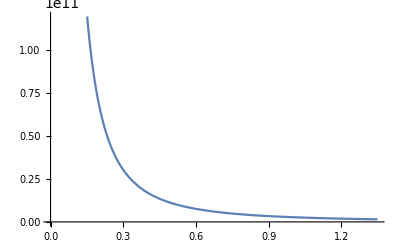

```mathematica
Plot[FillingFactor[x], {x, 0, x01b}]
```

```mathematica
FillingFactor[x01b]
```

1.30734×10^28

```mathematica
(*probando calcular el filling factor con ambas contribuciones*)
```

```mathematica
xinic := 1.3453*10^7
```

```mathematica
Mx=NDSolve[{y'[x]== mb*x*1/((1+x^2)^(1/2))+σ*x^2*1/((1+x^2)^(5/2))*y[x]^2,y[xi]==m0},y,{x,xinic,xi}, MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->40,AccuracyGoal->20]
```

{{y→InterpolatingFunction[…]}}

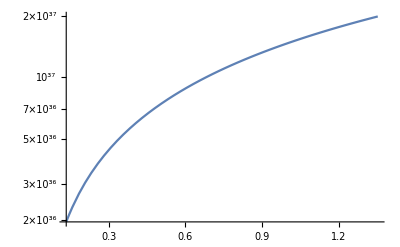

```mathematica
LogPlot[y[x]/.Mx, {x,xinic, xi},  PlotRange->All]
```

```mathematica
y[xinic]/.Mx
```

{1.95225×10^36}

```mathematica
AreaBH2[x_]:= (16*π*G)/c^4*(y[x]/.Mx)^2
```

```mathematica
FillingFactor2[x_]:= AreaBH2[x]/Σhyp[x]
```

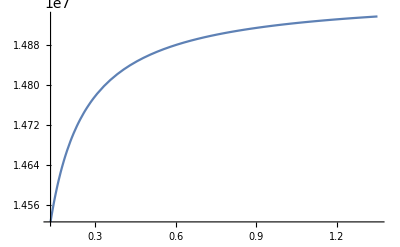

```mathematica
Plot[FillingFactor2[x], {x, xinic, xi}]
```